```mathematica
Needs["ErrorBarPlots`"];
```

The model

```mathematica
ParNames={"y0","x1","σ1","A","x2","σ2"};
Fixed={True,False,False,False,False,False};
StartValue={0,11,0.1,30,14,0.1};
ParMax=Length[ParNames];
UseErr=True;
```

```mathematica
f[x_,y0_,x1_,σ1_,A_,x2_,σ2_]:=y0+A/2*Erf[(x-x1)/(√2 σ1)]+A/2*Erf[-(x-x2)/(√2 σ2)];
```

Create and export dataset with pseudo-random errors for debugging
Compare to fit results of Origin with fit function GaussAmp

Import data
Columns: 1=x, 2=y, 3=yerr

```mathematica
XCol=1;
YCol=9;
YErrCol=10;
```

```mathematica
MyData=Import["D:/Temp/S_parameters_Delay007.tsv","Table"];
```

(* Activate the following to test the use of different columns *)
XCol = 2;
YCol = 3;
YErrCol = 4;
MyData = Transpose[Prepend[Transpose[MyData], Table[Random[], {51}]]]

```mathematica
Ind=1;
YCol=Piecewise[{{8,Ind==1}},9];
```

```mathematica
ShotNoise=(1+Part[MyData,All,YCol])^(1/2);
MyData=Transpose[Append[Transpose[MyData],ShotNoise]];
```

```mathematica
TheData[Ind]=MyData;
MinTime=Part[First[TheData[Ind]],XCol];
MaxTime=Part[Last[TheData[Ind]],XCol];
MinTime=11;
MaxTime=15;
If[Length[Transpose[TheData[Ind]]]==2||YErrCol==0,UseErr=False;];
```

```mathematica
TheData[Ind]=Select[TheData[Ind],MinTime≤Part[#1,XCol]≤MaxTime&];
```

```mathematica
X[TheTab_]:=Part[TheTab,All,XCol];
Y[TheTab_]:=Part[TheTab,All,YCol];
Err[TheTab_]:=Part[TheTab,All,YErrCol];
DataOnly[TheTab_]:=Part[TheTab,All,{XCol,YCol}];
DataAndErr[TheTab_]:=Table[{{Part[TheTab,Ind,XCol],Part[TheTab,Ind,YCol]},ErrorBar[Part[TheTab,Ind,YErrCol]]},{Ind,Length[TheTab]}];
WeightFunc[x_]:=x^-2;
MyWeights[TheTab_]:=WeightFunc[Part[TheTab,All,YErrCol]];
```

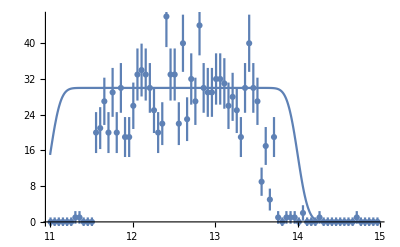

```mathematica
If[UseErr
,(DataPlot=ErrorListPlot[DataAndErr[TheData[Ind]],PlotRange->All]);
,(DataPlot=ListPlot[DataOnly[TheData[Ind]],PlotStyle->PointSize[0.02],PlotRange->All]);]
StartPlot=Plot[Apply[f,Prepend[StartValue,t]],{t,MinTime,MaxTime}];
Show[DataPlot,StartPlot]
```

```mathematica
ParamRepl=Table[P[x]->Part[ParNames,x],{x,ParMax}];
Q[x_]:=If[Part[Fixed,x],Part[StartValue,x],P[x]];
QQTab={};
Do[If[Not[Part[Fixed,x]],AppendTo[QQTab,{P[x],Part[StartValue,x]}]];,{x,ParMax}];
QQIndTab=Prepend[Table[Q[x],{x,ParMax}],t];
FitParIndTab=Prepend[Table[FitPar[x],{x,ParMax}],t];
```

```mathematica
TheFit[Ind]=
If[UseErr
,NonlinearModelFit[DataOnly[TheData[Ind]],Apply[f,QQIndTab],QQTab,t,MaxIterations->100,Weights->MyWeights[TheData[Ind]]]
,NonlinearModelFit[DataOnly[TheData[Ind]],Apply[f,QQIndTab],QQTab,t,MaxIterations->100]];
```

| Estimate | Standard Error | Confidence Interval
x1 | 11.5502 | 0.42687 | {10.6999,12.4006}
σ1 | 0.0108276 | 0.680632 | {-1.34506,1.36672}
A | 27.2216 | 0.920872 | {25.3871,29.056}
x2 | 13.5903 | 0.0206113 | {13.5492,13.6313}
σ2 | 0.108179 | 0.0228789 | {0.0626014,0.153756}

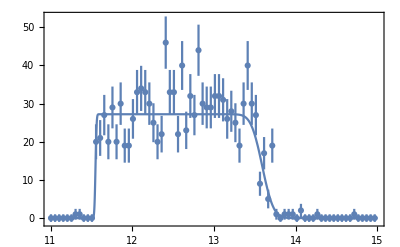

χ^2 = 81.9921        DoF = 75

χ^2/DoF = 1.09323

The fit residuals scatter MORE than (the most likely value of the PDF) expect from the error bars.

One needs to consider the following confidence interval to accomodate the fit residuals in a χ^2 distribution.

The 2.07612×10^-14 confidence interval (cutting off at equal values of the PDF).

The 0.456895 confidence interval (cutting off at equal values of the CDF, which is less standard).

A value near unity here implies that the fit residuals are unlikely to be explained by statistical scatter.

A value near zero here might be coincidence but it might also indicate that the dataset overestimated the error bars.

```mathematica
(*Do[
FitPar[x]=If[Part[Fixed,x],
Part[StartValue,x],
P[x]/.TheFit[Ind]["BestFitParameters"]];
,{x,ParMax}];*)
(*Print["File number : ",Ind];*)
Print[TheFit[Ind]["ParameterConfidenceIntervalTable"]/.ParamRepl];
FitPlot=Plot[TheFit[Ind][t],{t,MinTime,MaxTime},Frame->True];
Show[FitPlot,DataPlot,PlotRange->All]
NumberOfDataPoints=Length[TheData[Ind]];
NumberOfFreePars=Length[Cases[Fixed,False]];
DoF=NumberOfDataPoints-NumberOfFreePars;
ChiSq=Part[TheFit[Ind]["ANOVATable"],1,1,3,3];
If[UseErr&&DoF>0,Print["χ^2 = ",ChiSq,"        DoF = ",DoF];
Print["χ^2/DoF = ",ChiSq/DoF];
str1=If[ChiSq>DoF,"MORE","LESS"];
Print["The fit residuals scatter "<>str1<>" than (the most likely value of the PDF) expect from the error bars."];
PDFχsq[ν_,g_]:=Simplify[PDF[ChiSquareDistribution[ν],g],g>0];
CDFχsq[ν_,g_]:=Simplify[CDF[ChiSquareDistribution[ν],g],g>0];
(*PDFχsq[ν,g]*)
(*CDFχsq[ν,g]*)
gminP=g/.FindRoot[PDFχsq[DoF,g]==PDFχsq[DoF,ChiSq],{g,DoF/3}];
gmaxP=g/.FindRoot[PDFχsq[DoF,g]==PDFχsq[DoF,ChiSq],{g,3*DoF}];
probP=Max[Abs[CDFχsq[DoF,ChiSq]-CDFχsq[DoF,gminP]],Abs[CDFχsq[DoF,ChiSq]-CDFχsq[DoF,gmaxP]]];
Print["One needs to consider the following confidence interval to accomodate the fit residuals in a χ^2 distribution."];
Print["The ",probP," confidence interval (cutting off at equal values of the PDF)."];
gminC=g/.FindRoot[CDFχsq[DoF,g]==1-CDFχsq[DoF,ChiSq],{g,DoF}];
probC=Abs[CDFχsq[DoF,ChiSq]-CDFχsq[DoF,gminC]];
Print["The ",probC," confidence interval (cutting off at equal values of the CDF, which is less standard)."];
Print["A value near unity here implies that the fit residuals are unlikely to be explained by statistical scatter."];
Print["A value near zero here might be coincidence but it might also indicate that the dataset overestimated the error bars."];
]
```

```mathematica
(* The following should evaluate to χ^2 *)
(*Total[((TheFit[Ind]["FitResiduals"])/Err[TheData[Ind]])^2]*)
```

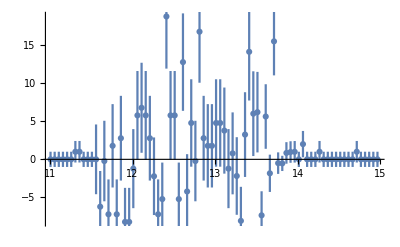

```mathematica
If[UseErr,
Residuals=TheFit[Ind]["FitResiduals"];
ResidualsAndErr[TheTab_]:=Table[{{Part[TheTab,Ind2,XCol],Part[Residuals,Ind2]},ErrorBar[Part[TheTab,Ind2,YErrCol]]},{Ind2,Length[TheTab]}];
ErrorListPlot[ResidualsAndErr[TheData[Ind]],PlotRange->All]
]
```

```mathematica
ExpPoints=200;
ExpTab=Table[{t,TheFit[Ind][t]},{t,MinTime,MaxTime,(MaxTime-MinTime)/ExpPoints}];
ExpName="D:/Temp/Erf-fit"<>ToString[Ind]<>".txt";
Export[ExpName,SetPrecision[ExpTab,6],"Table"]
```

D:/Temp/Erf-fit1.txt